# ２次曲線

## ２次曲線のパラメータ表示

### （１）楕円

#### 定義式（標準形）

```mathematica
x^2/a^2+y^2/b^2==1
```

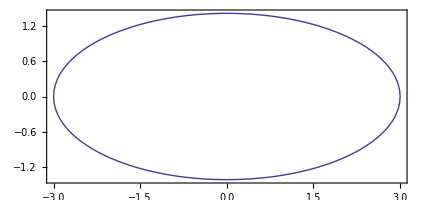

```mathematica
a=3;
b=Sqrt[2];
ContourPlot[x^2/a^2+y^2/b^2==1,{x,-a,a},{y,-b,b},AspectRatio->Automatic]
```

#### パラメータ表示

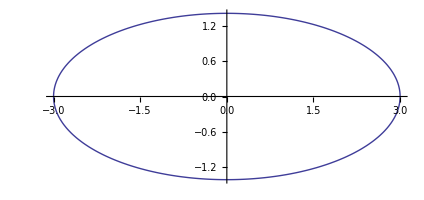

```mathematica
a=3;
b=Sqrt[2];
ParametricPlot[{a*Cos[t],b*Sin[t]},{t,0,2Pi}]
```

#### パラメータの幾何的意味

```mathematica
a=3;
b=Sqrt[2];
Manipulate[
Show[
ParametricPlot[{a*Cos[t],b*Sin[t]},{t,0,2Pi},PlotRange->{-Max[a,b]-0.5,Max[a,b]+0.5},PlotStyle->Thick],
Graphics[{
Circle[{0,0},a],
Circle[{0,0},b],
Circle[{0,0},0.4,{0,s}],
Text["(a cos θ, b sin θ)",{a*Cos[s],b*Sin[s]}+{0.8,0.2}],
Text["(a cos θ, a sin θ)",{a*Cos[s],a*Sin[s]}+{0.8,0.2}],
Text["(b cos θ, b sin θ)",{b*Cos[s],b*Sin[s]}+{0.8,-0.2}],
Text["θ",{0.5*Cos[s/2],0.5*Sin[s/2]}],
PointSize[0.02],
Point[{a*Cos[s],b*Sin[s]}],
Point[{a*Cos[s],a*Sin[s]}],
Point[{b*Cos[s],b*Sin[s]}],
Line[{{Max[a,b]*Cos[s],Max[a,b]*Sin[s]},{0,0}}],
Dashed,
Line[{{a*Cos[s],a*Sin[s]},{a*Cos[s],b*Sin[s]},{b*Cos[s],b*Sin[s]}}]
}]
],{{s,Pi/3,"θ"},0,2Pi},SaveDefinitions->True]
```

### （２）双曲線

#### 定義式（標準形）

```mathematica
x^2/a^2-y^2/b^2==1
```

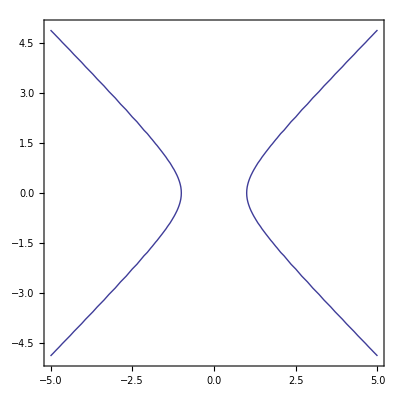

```mathematica
c=1;
d=1;
ContourPlot[x^2/c^2-y^2/d^2==1,{x,-5*c,5*c},{y,-5*d,5*d},AspectRatio->Automatic]
```

#### 漸近線

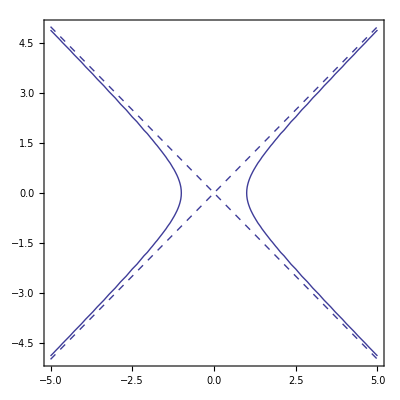

```mathematica
c=1;
d=1;
Show[
ContourPlot[x^2/c^2-y^2/d^2==1,{x,-5*c,5*c},{y,-5*d,5*d},AspectRatio->Automatic],
Plot[d/c x,{x,-5*c,5*c},PlotStyle->Dashed],
Plot[-d/c x,{x,-5*c,5*c},PlotStyle->Dashed]
]
```

#### パラメータ表示

```mathematica
c=1;
d=1;
ParametricPlot[{c*Sec[t],d*Tan[t]},{t,-Pi/2,Pi/2}]
```

-Graphics-

```mathematica
c=1;
d=1;
ParametricPlot[{
{c*Sec[t],d*Tan[t]},
{-c*Sec[t],d*Tan[t]}
},{t,-Pi/2,Pi/2}]
```

-Graphics-

#### パラメータの幾何的意味

```mathematica
c=1;
d=1/Sqrt[2];
Manipulate[
Show[
ParametricPlot[{
{c*Sec[t],d*Tan[t]},
{-c*Sec[t],d*Tan[t]}
},{t,-Pi/2.5,Pi/2.5}],
Graphics[{
Point[{c*Sec[s],0}],
Point[{d,d*Tan[s]}],
Point[{d,0}],
PointSize[0.02],
Point[{c*Sec[s],d*Tan[s]}],
Point[{c*Cos[s],c*Sin[s]}],
Text["(c sec θ, d tan θ)",{c*Sec[s],d*Tan[s]}+{0,0.2}],
Text["(c cos θ, c sin θ)",{c*Cos[s],c*Sin[s]}+{-0.6,0.2}],
Text["(d,0)",{d,0}+{0,-0.2}],
Text["(d, d tan θ)",{d,d*Tan[s]}+{0,0.2}],
Text["θ",{0.3*Cos[s/2],0.3*Sin[s/2]}],
Circle[{0,0},c],
Circle[{0,0},0.2,{0,s}],
Line[{{0,0},{c*Cos[s],c*Sin[s]}}],
Dashed,
Line[{{c*Sec[s],d*Tan[s]},{c*Sec[s],0},{c*Cos[s],c*Sin[s]},{d,d*Tan[s]},{d,0}}]
}]
],{s,0,Pi/2.5},SaveDefinitions->True]
```

#### 別のパラメータ表示

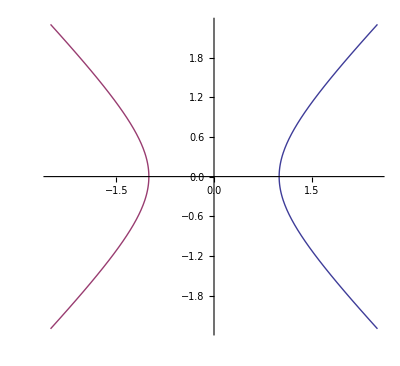

```mathematica
c=1;
d=1;
ParametricPlot[{{c*Cosh[t],d*Sinh[t]},{-c*Cosh[t],d*Sinh[t]}},{t,-Pi/2,Pi/2}]
```

### （３）放物線

#### 定義式（標準形）

```mathematica
y^2==4*p*x
```

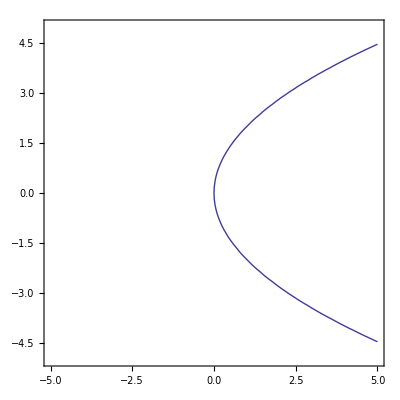

```mathematica
p=1;
ContourPlot[y^2==4*p*x,{x,-5,5},{y,-5,5}]
```

#### パラメータ表示

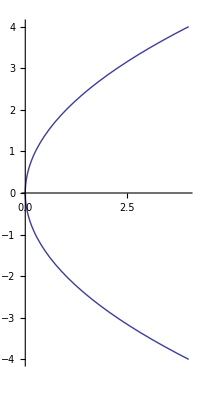

```mathematica
p=1;
ParametricPlot[{p*t^2,2*p*t},{t,-2,2}]
```